# Trägheitsmoment

```mathematica
ClearAll["Global`*"]
```

## Aufgabe 1

### 1

```mathematica
T = #/10&/@{13.0, 12.9, 12.9, 12.95, 12.9, 13.0, 12.8, 12.85, 12.95, 12.9};
```

```mathematica
r = 40.0/2/1000;
```

```mathematica
m=0.6;
```

```mathematica
T0 = Mean[T]
```

1.2915

### 2

```mathematica
T = #/10&/@{25.5, 25.1, 25.1, 25.05, 25.25, 25.55, 25.3, 25.3, 25.55, 25.45};
```

```mathematica
d=0.06;
```

```mathematica
m=0.3;
```

```mathematica
T6 = Mean[T]
```

2.5315

### Tisch

```mathematica
k=8*m*d^2*π^2/(T6^2-T0^2)
```

0.0179882

```mathematica
T = #/10&/@{11.85, 11.7, 12.0, 11.8, 11.7, 11.8, 11.9, 11.8, 11.95, 11.7};
```

```mathematica
Tt = Mean[T]
```

1.182

```mathematica
Jt= Tt^2*k/(4π^2)
```

0.000636594

### Fehler

```mathematica
Sqrt[0.64*π^4*m^2*d^4/(T6^2-T0^2)^3]
```

0.00082618

## Aufgabe 2

### Quader

```mathematica
h=2/100;
```

```mathematica
b=2/100;
```

```mathematica
l=7/100;
```

```mathematica
mq=0.235;
```

```mathematica
T=#/10&/@{12.7, 12.8, 13.0, 12.95, 12.65, 12.7, 12.95, 12.7, 12.7, 12.85};
```

```mathematica
Tq=Mean[T]
```

1.28

```mathematica
Jq= Tq^2*k/(4*π^2)-Jt
```

0.000109936

```mathematica
Jqt = mq/12*(b^2+l^2)
```

0.000103792

### Scheibe

```mathematica
r=0.05;
```

```mathematica
ms=0.3;
```

```mathematica
T=#/10&/@{14.95, 15.1, 14.6, 15.0, 15.15, 15.05, 15.1, 15.1, 15.0, 15.0};
```

```mathematica
Ts=Mean[T]
```

1.5005

```mathematica
Js =Ts^2*k/(4*π^2)-Jt
```

0.000389293

```mathematica
Jst = ms*r^2/2
```

0.000375

### Fehler

```mathematica
Sqrt[0.0025*Ts^2k^2/(4π^2)]
```

0.00021479

```mathematica
Sqrt[0.0025*Tq^2k^2/(4π^2)]
```

0.000183226

## Aufgabe 3

```mathematica
m = 0.3;
```

```mathematica
r=0.02;
```

```mathematica
T = {{12.4, 12.3, 12.4, 12.65, 12.45},
	{12.55, 12.7, 12.75, 12.7, 12.55},
	{12.4, 13.55, 13.25, 13.4, 13.25},
	{14.5, 14.5, 14.4, 14.5, 14.5},
	{16, 15.8, 15.8, 16, 16.05},
	{17.6, 17.55, 17.7,  17.65, 17.5},
	{19.35, 19.5, 19.7, 19.45, 19.45}};
```

```mathematica
T = Mean[#]/10&/@T;
```

```mathematica
yd= Table[T[[d]]^2,{d,1,Length[T]}];
```

```mathematica
xd = Table[((d-1)/100)^2,{d,1,Length[T]}];
```

```mathematica
sxy = 1/(Length[T]-1)*∑_(i=1)^Length[T] ((xd[[i]]-Mean[xd])(yd[[i]]-Mean[yd]))//N
```

0.00114723

```mathematica
sx = 1/(Length[T]-1)*∑_(i=1)^Length[T] ((xd[[i]]-Mean[xd])^2)//N
```

1.82×10^-6

```mathematica
y[x_] = sxy/sx(x-Mean[xd])+Mean[yd]
```

2.34469+630.349 (-13/10000+x)

```mathematica
y[0]
```

1.52523

```mathematica
reg = Plot[y[x], {x, 0, 0.004}];
```

```mathematica
listplot = ListPlot[ Table[{((d-1)/100)^2,T[[d]]^2},{d,1,Length[T]}]];
```

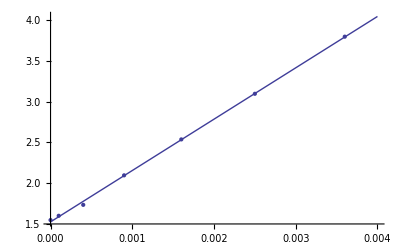

```mathematica
Show[reg, listplot]
```

```mathematica
J = #^2*k/(4π^2)-Jt&/@T
```

{0.0000685347,0.0000925422,0.000153719,0.000318761,0.000519676,0.000774815,0.00109422}

Kontrollrechnung

```mathematica
1/2*0.3*0.02^2
```

0.00006

```mathematica
Jst= Table[J[[1]]+m*(d/100)^2, {d, 1, 6}]
```

{0.0000985347,0.000188535,0.000338535,0.000548535,0.000818535,0.00114853}

```mathematica
err = Table[Jst[[d]] - J[[d+1]], {d, 1, 6}]
```

{5.99246×10^-6,0.0000348156,0.0000197737,0.0000288588,0.0000437192,0.0000543108}

```mathematica
Table[err[[d]]/J[[d+1]], {d, 1, 6}]//N
```

{0.0647538,0.226488,0.0620329,0.0555322,0.0564253,0.049634}

Kontrollrechnung

```mathematica
m/k*(4π^2)
```

658.406

```mathematica
Table[Sqrt[0.0025*T[[t]]^2k^2/(4π^2)], {t, 1, Length[T]}]
```

{0.000178073,0.000181079,0.000188523,0.000207275,0.000228031,0.000251936,0.000278991}